## Task 2 List Generation

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task2_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

Import::nffil: File task2_data.dat not found during Import.

```mathematica
dataList=Table[StringTake[data[[i]],6],{i,1,Length[data]}];
```

{{110100,2877},{010101,2845},{011100,2808},{011101,276},{001100,79},{100100,69},{000101,86},{110001,7},{011000,73},{010100,60},{110101,297},{111100,283},{010001,87},{110000,86},{100110,1},{001010,10},{111000,8},{101100,6},{001101,3},{011001,6},{100101,7},{000100,2},{000011,10},{100010,6},{000111,1},{010000,1},{101010,1},{001011,2},{000001,1},{001000,1},{100000,1}}

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
000001 | 1
000111 | 1
001000 | 1
010000 | 1
100000 | 1
100110 | 1
101010 | 1
000100 | 2
001011 | 2
001101 | 3
011001 | 6
100010 | 6
101100 | 6
100101 | 7
110001 | 7
111000 | 8
000011 | 10
001010 | 10
010100 | 60
100100 | 69
011000 | 73
001100 | 79
000101 | 86
110000 | 86
010001 | 87
011101 | 276
111100 | 283
110101 | 297
011100 | 2808
010101 | 2845
110100 | 2877

## Task1-2 (The bit-string order is Reversed!)

```mathematica
graph={{0.3461717838632017,1.4984640297338632},{0.6316400411846113,2.5754677320579895},{1.3906262250927481,2.164978861396621},{0.66436005100802,0.6717919819739032},{0.8663329771713457,3.3876341010035995},{1.1643107343501296,1.0823066243402013}}
```

{{0.346172,1.49846},{0.63164,2.57547},{1.39063,2.16498},{0.66436,0.671792},{0.866333,3.38763},{1.16431,1.08231}}

```mathematica
labels={"1","2","3","4","5","6"};
```

```mathematica
solutions={{1,3,5},{3,4,5},{3,5,6}};
solLabels={"101010","001110","001011"};
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=1;
color1=Lighter[Gray];
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1]};bList={#}&/@graph;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph[[#]],T]}&/@Table[i,{i,1,6}];
dots={Black,Disk[graph[[#]],0.05]}&/@Table[i,{i,1,6}];
Graphics[Flatten[{circles,dots},1],Frame->True,FrameTicks->None,PlotLabel->Style[ToString[solLabels[[i1]]],Bold,25,Black]]]
```

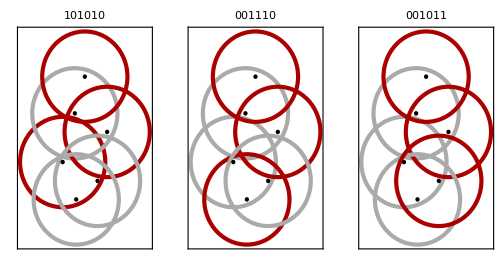

```mathematica
GraphicsRow[{plot[1],plot[2],plot[3]},ImageSize->500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["101010c.jpg",plot[1]]
Export["001110c.jpg",plot[2]]
Export["001011c.jpg",plot[3]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

101010c.jpg

001110c.jpg

001011c.jpg

## Task 3 List Generation

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
data=Import["task3_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

```mathematica
dataList=Table[StringTake[data[[i]],12],{i,1,Length[data]}];
```

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

## Task 2 Visualization (The bit-string order is Reversed!)

```mathematica
graph1={{1.19,4.25},{2.71,3.48},{1.19,3.51},{2,3.38},{1.12,2.86},{1.70,2.42},{2.36,2.54},{1.52,1.48},{2.15,1.54},{2.14,1.87},{1.72,0.86},{2.29,0.87}};
solLabels={"011000010011","101000010011","100001010011","010001010011"};
Do[f[j]={},{j,1,4}];
Do[If[StringPart[solLabels[[j]], i]=="1",f[j]=Append[f[j],13-i]],{i,1,12},{j,1,4}]
solutions=Table[f[j],{j,1,4}]
```

{{11,10,5,2,1},{12,10,5,2,1},{12,7,5,2,1},{11,7,5,2,1}}

```mathematica
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.5;
color1=Lighter[Gray];
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,12}];
dots={Black,Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,12}];
Graphics[Flatten[{circles,dots},1],Frame->True,FrameTicks->None]]
```

{{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.7,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}}

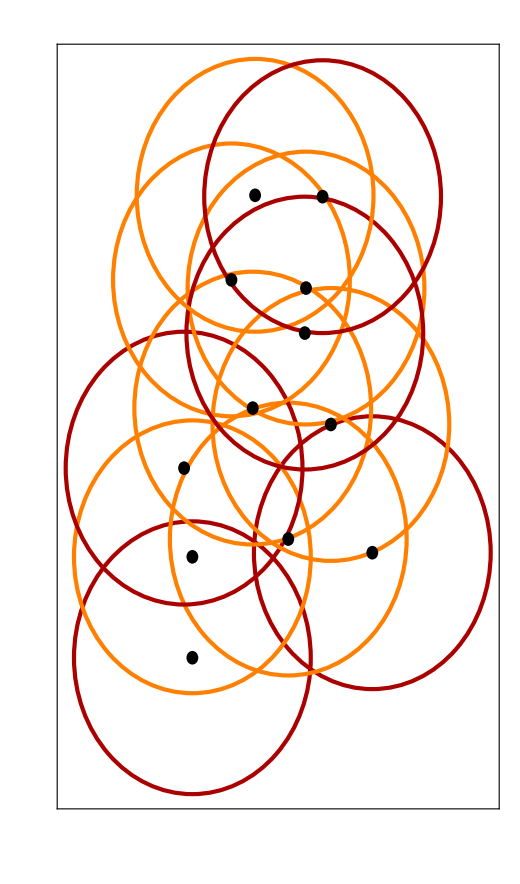
-Graphics--Graphics-

```mathematica
Img=-Graphics-;
Img=ImageAdjust[Img,{0,4}];
graph1={{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.70,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}}
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=1;
color1=Orange;
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,12}];
dots={Black,Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,12}];
Graphics[
Flatten[{circles,dots},1],Frame->True,FrameTicks->None,ImageSize->520,AspectRatio->1.7]]
image=Overlay[{Img,plot[2]},Alignment->Center]
```

```mathematica
Export["overlay.jpg",image]
```

overlay.jpg

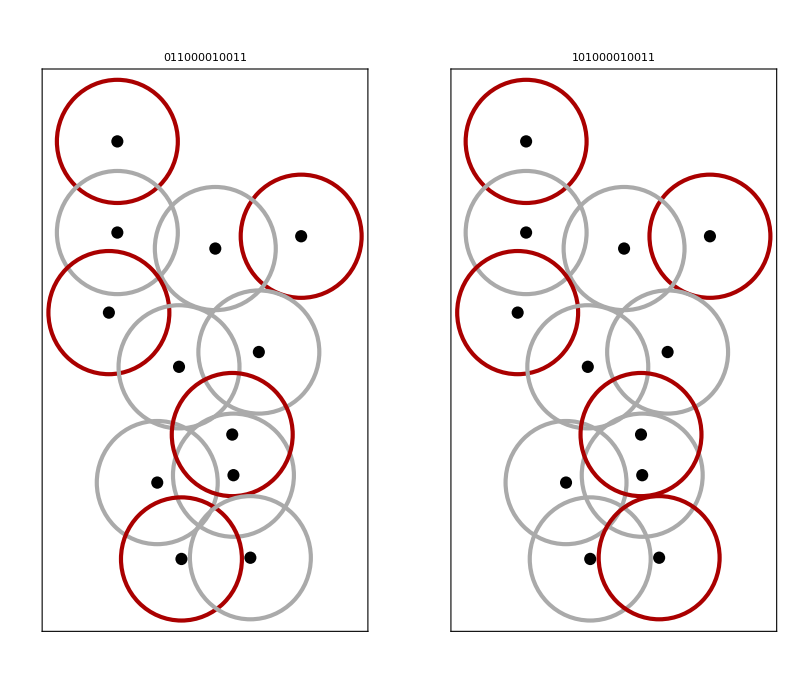

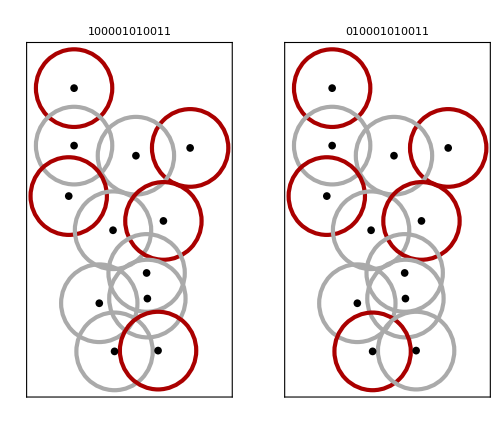

```mathematica
GraphicsRow[{plot[1],plot[2]},ImageSize->500]
GraphicsRow[{plot[3],plot[4]},ImageSize->500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["011000010011c.jpg",plot[1]]
Export["101000010011c.jpg",plot[2]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

011000010011c.jpg

101000010011c.jpg

## Business Solution

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task4_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

Import::nffil: File task4_data.dat not found during Import.

```mathematica
dataList=Table[StringTake[data[[i]],13],{i,1,Length[data]}];
```

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

```mathematica
Length[graph2]
```

13

```mathematica
graph2={{40.77912258043522,-73.98454494478796},{40.77574281493932,-73.99038143102224},{40.76898276810238,-73.98042507215202},{40.765862514512946,-73.99724788541549},{40.76274211441795,-73.98523159022729},{40.762482074463655,-73.9776784903947},{40.75832129683225,-73.9869482038256},{40.75780118131573,-73.99930782173348},{40.75494047323415,-73.99450130365818},{40.75364011068508,-73.97561855407673},{40.74687781544779,-73.97252864959975},{40.74557729521456,-74.00411433980875}};
```

```mathematica
solLabels={"1010111011101","1011011011101","1100101111011"};
Do[f[j]={},{j,1,4}];
Do[If[StringPart[solLabels[[j]], i]=="1",f[j]=Append[f[j],14-i]],{i,1,13},{j,1,3}]
solutions=Table[f[j],{j,1,3}]
```

{{13,11,9,8,7,5,4,3,1},{13,11,10,8,7,5,4,3,1},{13,12,9,7,6,5,4,2,1}}

```mathematica
solutions[[1]]
```

```mathematica
{13,11,10}
```

-Graphics-

```mathematica
rs=75;
s1=1.35*rs;
s2=0.8*1*rs;
s3=1.15*rs;
Show[GeoListPlot[GeoPosition[#]&/@graph2[[{2,3}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Black],
GeoListPlot[GeoPosition[#]&/@graph2[[{3}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Red],

GeoListPlot[GeoPosition[#]&/@graph2[[{4,5,6}]],PlotMarkers->{"◯",Scaled[s2]},PlotStyle->Black],
GeoListPlot[GeoPosition[#]&/@graph2[[{4,5}]],PlotMarkers->{"◯",Scaled[s2]},PlotStyle->Red],

GeoListPlot[GeoPosition[#]&/@graph2[[{10,11,12,13}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Black],
GeoListPlot[GeoPosition[#]&/@graph2[[{11,13}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Red],

GeoListPlot[GeoPosition[#]&/@graph2[[{7,8,9}]],PlotMarkers->{"◯",Scaled[s3]},PlotStyle->Red]
]
```

-Graphics-

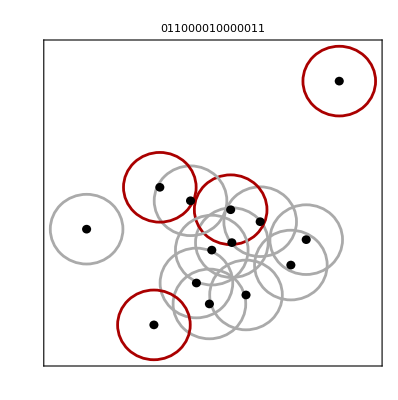

```mathematica
plot[1]
```

## Business Solution 2

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics\\data Task3 ext"]
data1=Import[#,{"List","List"}]&/@FileNames["*.dat"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics\data Task3 ext

```mathematica
Clear[dataList]
dataList[j_]:=Table[StringTake[data1[[j]][[i]],13],{i,1,Length[data1[[j]]]}]
Block[{t=Take[SortBy[Tally[dataList[1]],Last],-20]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
0011000000110 | 47
0110001010011 | 47
1011000010011 | 47
0101000000110 | 49
1100001010011 | 64
1110000010011 | 71
0011000011001 | 180
0101000011001 | 189
1000010011001 | 290
0000101010011 | 291
0000011010011 | 383
1010000011001 | 395
1100000011001 | 422
0101000010011 | 745
0010001010011 | 789
0011000010011 | 795
0100001010011 | 797
1000010010011 | 894
1100000010011 | 1000
1010000010011 | 1014

```mathematica
Take[SortBy[Tally[dataList[1]],Last],-4][[All,1]]
```

{0100001010011,1000010010011,1100000010011,1010000010011}

```mathematica
Table[StringCount[Take[SortBy[Tally[dataList[i]],Last],-4][[All,1]],"1"],{i,1,Length[data1]}]
```

{{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,6},{5,5,5,5},{5,5,5,6},{5,5,5,6},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,6},{7,6,6,6},{5,5,5,5},{5,5,5,5},{5,5,5,5},{5,5,5,5}}

```mathematica
Total[Total[Table[StringCount[StringTake[Take[SortBy[Tally[dataList[i]],Last],-4][[All,1]],1],"1"],{i,1,Length[data1]}]]]
Total[48*4]
%%/%//N
```

55

192

0.286458

```mathematica
Clear[solLabels,solLabelGen]
index=1;
solLabels[j_]:=Take[SortBy[Tally[dataList[j]],Last][[All,1]],-4];
```

```mathematica
solLabelGen[index_]:=Module[{f,solutions},
Do[f[j]={},{j,1,4}];
Do[If[StringPart[solLabels[index][[j]], i]=="1",f[j]=Append[f[j],14-i]],{i,1,13},{j,1,4}];
solutions=Table[f[j],{j,1,4}];
solutions
]
```

```mathematica
Count[Flatten[Table[solLabelGen[i],{i,1,48}]],13]
```

55

# Location

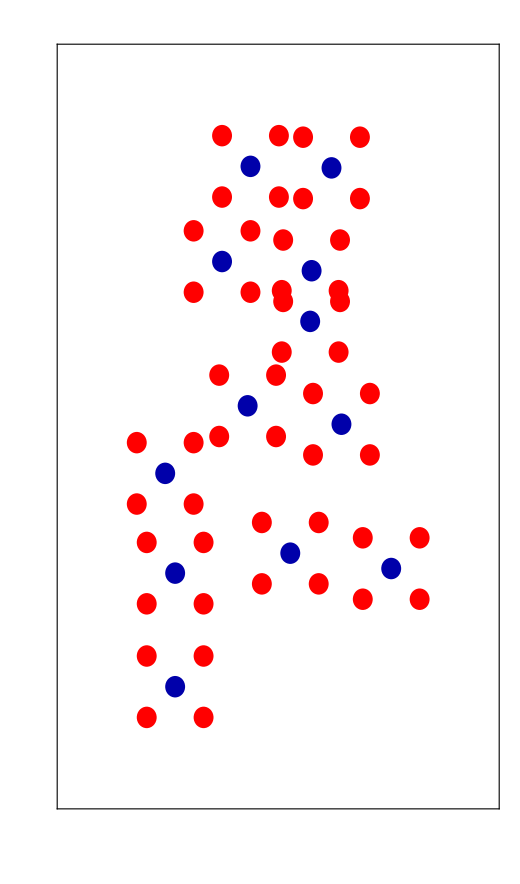
-Graphics--Graphics-

```mathematica
Img=-Graphics-;
Img=ImageAdjust[Img,{0,4}];
graph1={{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.70,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}};
direction={{0.2,0.2},{0.2,-0.2},{-0.2,0.2},{-0.2,-0.2}};
dat1=Table[graph1[[i]]+direction[[j]],{i,1,12},{j,1,4}];
graph1=Flatten[{{graph1},dat1},2];
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.5;
color1=Orange;
color2=Darker[Red];
colorList=Table[If[MemberQ[solutions[[i1]],i],color2,color1],{i,1,60}];bList={#}&/@graph1;
circles={colorList[[#]],Opacity[0],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,60}];
dots={If[#>= 13,Red,Darker[Blue]],Disk[graph1[[#]],0.07]}&/@Table[i,{i,1,60}];
Graphics[
Flatten[{circles,dots},1],Frame->True,FrameTicks->None,ImageSize->520,AspectRatio->1.7]]
image=Overlay[{Img,plot[1]},Alignment->Center]
```

```mathematica
Export["mapping(12+1).jpg",image]
```

mapping(12+1).jpg

# dd

```mathematica
solLabelGen[1]
```

{{12,7,5,2,1},{13,8,5,2,1},{13,12,5,2,1},{13,11,5,2,1}}

```mathematica
Block[{t=Take[SortBy[Tally[dataList[16]],Last],-20]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
1011001010010 | 63
1000001010010 | 66
0101001010011 | 67
0000001010011 | 70
1101000011000 | 212
0101000011001 | 230
0011000011001 | 241
1011000011000 | 258
1011000010010 | 525
1101000010010 | 532
0000011010011 | 546
1000011010010 | 550
0011000010011 | 559
0000101010011 | 560
0101000010011 | 576
1000101010010 | 614
1010001010010 | 725
0100001010011 | 779
1100001010010 | 785
0010001010011 | 796

{10,10,10,10,11,11,11,11,1,12,12,12,12,1,1,1,2,2,2,2,3,3,3,3,4,4,4,4,5,5,5,5,6,6,6,6,7,7,7,7,8,8,8,8,9,9,9,9}

{1,2,3,4,1,2,3,4,1,1,2,3,4,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}

```mathematica
Img=-Graphics-;
Do[
index=9;
graphindex=ToExpression[StringReplace[StringTake[StringTake[FileNames["*.dat"],{-7,-5}],2],"a"->""]][[index]];
directionindex=ToExpression[StringTake[StringTake[FileNames["*.dat"],{-7,-5}],-1]][[index]];
solutions=solLabelGen[index];
Img=ImageAdjust[Img,{0,4}];
graph1={{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.70,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}};
direction={{0.2,0.2},{0.2,-0.2},{-0.2,0.2},{-0.2,-0.2}};
dat1=graph1[[graphindex]]+direction[[directionindex]];
graph1=Append[graph1,dat1];
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.5;
color1=Orange;
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1],If[MemberQ[solutions[[i1]],13],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,13}];
dots={If[#==13,Red,Blue],Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,13}];
Graphics[
Flatten[{circles,dots},1],Frame->True,FrameTicks->None,ImageSize->520,AspectRatio->1.7]]
ima[directionindex]=Overlay[{Img,plot[1]},Alignment->Center]
,{index,{9,14,15,16}}]
```

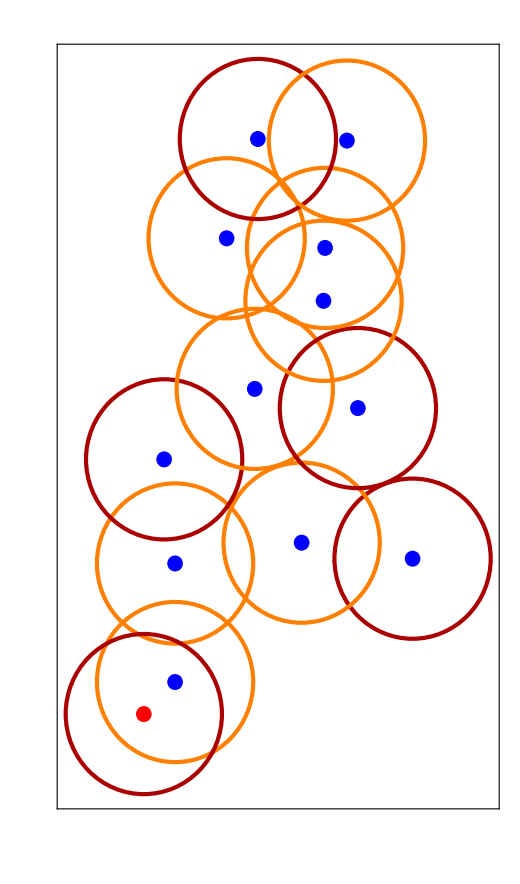
-Graphics--Graphics-

```mathematica
ima[4]
```

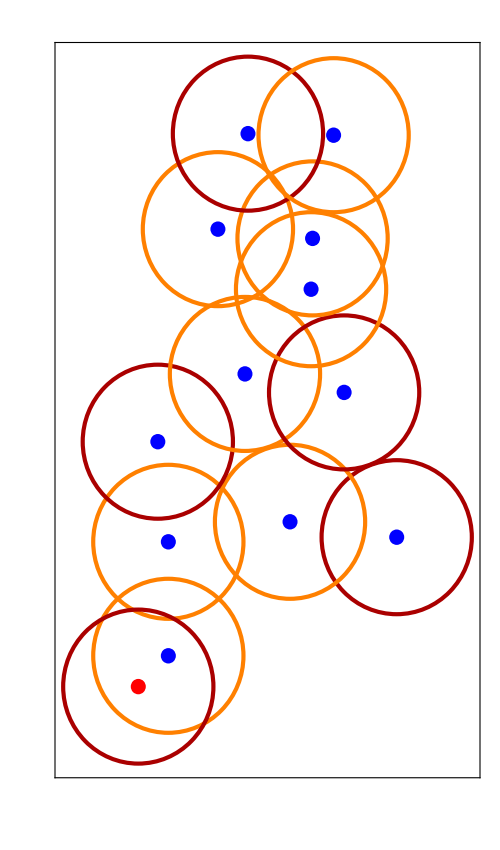
-Graphics--Graphics-

```mathematica
ima[4]
```

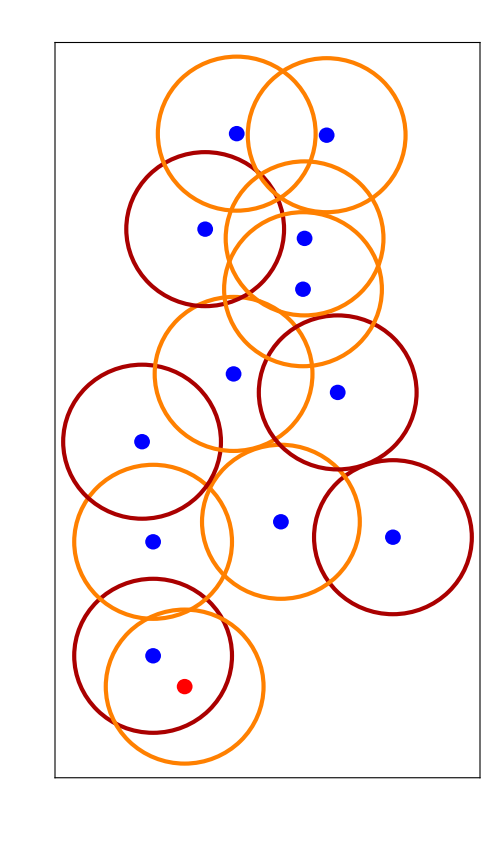
-Graphics--Graphics-

```mathematica
ima[2]
```

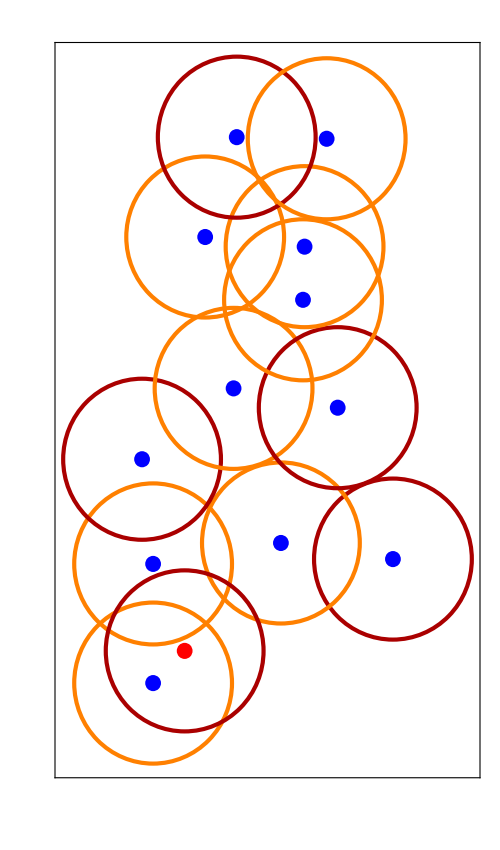
-Graphics--Graphics-

```mathematica
ima[1]
```

```mathematica
Block[{t=Take[SortBy[Tally[dataList[-5]],Last],-20]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
1101000000110 | 14
1101000010010 | 19
0101000010011 | 20
1100000011001 | 20
1001000011001 | 23
1100000100110 | 25
0010001000110 | 28
1100001000110 | 41
1001000010011 | 43
0101000011001 | 46
1100000101001 | 79
1100001000011 | 83
0010001010011 | 97
1100000010011 | 103
1101001010011 | 103
0011000010011 | 175
1101000011011 | 181
1101000011001 | 1768
1100001010011 | 2877
1101000010011 | 3989

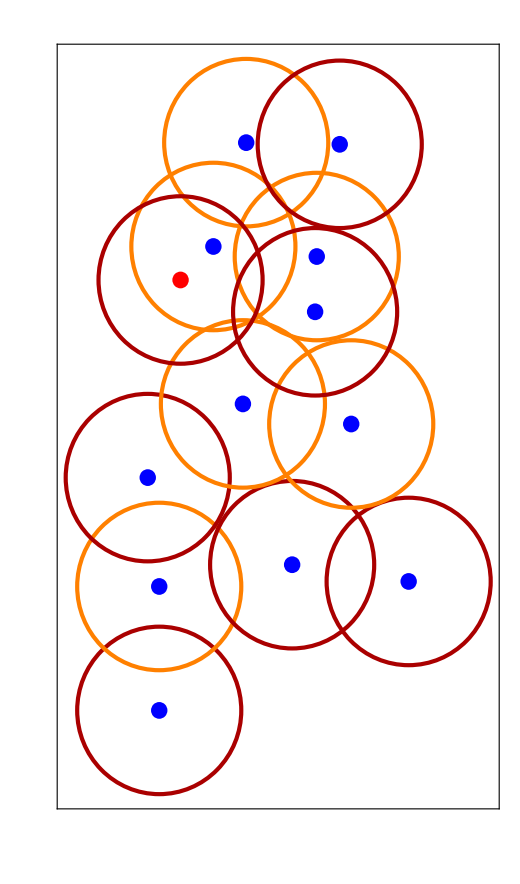
-Graphics--Graphics-

```mathematica
Img=-Graphics-;

index=-5;
graphindex=ToExpression[StringReplace[StringTake[StringTake[FileNames["*.dat"],{-7,-5}],2],"a"->""]][[index]];
directionindex=ToExpression[StringTake[StringTake[FileNames["*.dat"],{-7,-5}],-1]][[index]];
solutions=solLabelGen[index];
Img=ImageAdjust[Img,{0,4}];
graph1={{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.70,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}};
direction={{0.2,0.2},{0.2,-0.2},{-0.2,0.2},{-0.2,-0.2}};
dat1=graph1[[graphindex]]+direction[[directionindex]];
graph1=Append[graph1,dat1];
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.5;
color1=Orange;
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1],If[MemberQ[solutions[[i1]],13],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,13}];
dots={If[#==13,Red,Blue],Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,13}];
Graphics[
Flatten[{circles,dots},1],Frame->True,FrameTicks->None,ImageSize->520,AspectRatio->1.7]]
ima[directionindex]=Overlay[{Img,plot[1]},Alignment->Center]
```

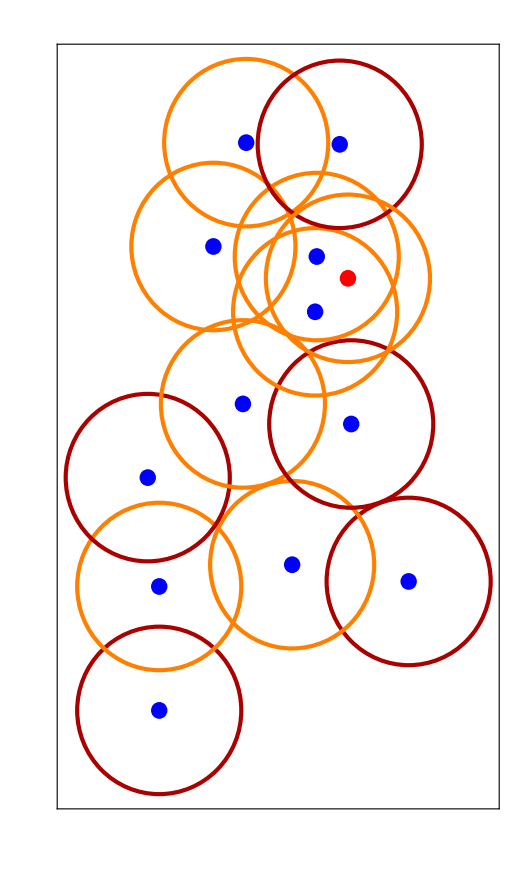
-Graphics--Graphics-

```mathematica
Img=-Graphics-;

index=1;
graphindex=ToExpression[StringReplace[StringTake[StringTake[FileNames["*.dat"],{-7,-5}],2],"a"->""]][[index]];
directionindex=ToExpression[StringTake[StringTake[FileNames["*.dat"],{-7,-5}],-1]][[index]];
solutions=solLabelGen[index];
Img=ImageAdjust[Img,{0,4}];
graph1={{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.70,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}};
direction={{0.2,0.2},{0.2,-0.2},{-0.2,0.2},{-0.2,-0.2}};
dat1=graph1[[graphindex]]+direction[[directionindex]];
graph1=Append[graph1,dat1];
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.5;
color1=Orange;
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1],If[MemberQ[solutions[[i1]],13],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,13}];
dots={If[#==13,Red,Blue],Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,13}];
Graphics[
Flatten[{circles,dots},1],Frame->True,FrameTicks->None,ImageSize->520,AspectRatio->1.7]]
ima[directionindex]=Overlay[{Img,plot[1]},Alignment->Center]
```